```mathematica
Clear["Global`*"]
```

# Resolvenet Method and Downfolding

## Definition

```mathematica
Downfold[matrix_,k_]:=Module[{C,C11,C12,C21,C22,M,P,Q,R,Rinv,U,V,W,indicesToDrop,indicesToKeep},
indicesToKeep=Range[k];
indicesToDrop=Complement[Range[Length[matrix]],indicesToKeep];
C11=matrix[[indicesToKeep,indicesToKeep]];
C12=matrix[[indicesToKeep,indicesToDrop]];
C21=matrix[[indicesToDrop,indicesToKeep]];
C22=matrix[[indicesToDrop,indicesToDrop]];
M=C11+C12.Inverse[ϵ IdentityMatrix@Length@C22-C22].C21;
M//Chop//Simplify];
```

```mathematica
H00=Module[{m,U},
m=DiagonalMatrix[{1,2,2}];
U=RandomVariate[CircularUnitaryMatrixDistribution[3]];
ConjugateTranspose[U].m.U//Chop
];
T01 =RandomVariate[CircularUnitaryMatrixDistribution[3]];
T10=ConjugateTranspose[T01];
H11=Module[{m,U},
m=DiagonalMatrix[{5,6,6}];
U=RandomVariate[CircularUnitaryMatrixDistribution[3]];
ConjugateTranspose[U].m.U//Chop
];
```

```mathematica
H=ArrayFlatten[{{H00,T01},{T10,H11}}];H//MatrixForm
```

(1.5896 | 0.160089-0.23578 ⅈ | 0.343467-0.206838 ⅈ | -0.087891-0.375298 ⅈ | 0.576458-0.138411 ⅈ | -0.131923+0.694667 ⅈ
0.160089+0.23578 ⅈ | 1.80209 | -0.25281-0.116642 ⅈ | -0.376147+0.366457 ⅈ | -0.238341+0.632632 ⅈ | 0.133052+0.49949 ⅈ
0.343467+0.206838 ⅈ | -0.25281+0.116642 ⅈ | 1.60831 | -0.746414-0.136072 ⅈ | 0.400099+0.177287 ⅈ | -0.0684913-0.47765 ⅈ
-0.087891+0.375298 ⅈ | -0.376147-0.366457 ⅈ | -0.746414+0.136072 ⅈ | 5.79983 | 0.0927303-0.209241 ⅈ | -0.269933+0.1867 ⅈ
0.576458+0.138411 ⅈ | -0.238341-0.632632 ⅈ | 0.400099-0.177287 ⅈ | 0.0927303+0.209241 ⅈ | 5.73832 | 0.320211+0.195677 ⅈ
-0.131923-0.694667 ⅈ | 0.133052-0.49949 ⅈ | -0.0684913+0.47765 ⅈ | -0.269933-0.1867 ⅈ | 0.320211-0.195677 ⅈ | 5.46185)

```mathematica
{Eigenvalues[H00],Eigenvalues[H11]}
```

{{2.,2.,1.},{6.,6.,5.}}

```mathematica
Heff=Downfold[H,3];
```

```mathematica
Heff/.ϵ->1.//Eigenvalues
```

{1.8,1.75545,0.794547}

```mathematica
Heff/.ϵ->2.//Eigenvalues
```

{1.75,1.67604,0.740624}

```mathematica
Eigenvalues[H]
```

{6.23607,6.19718,5.29589,1.76393,1.70411,0.802818}

```mathematica
nestFind[i_,n_]:=NestList[Sort[Eigenvalues@Heff/.ϵ->#][[i]]&,1,n]
```

```mathematica
nestFind[1,3]
```

{1,0.794547,0.802932,0.802603}

```mathematica
nestFind[2,3]
```

{1,1.75545,1.69988,1.70481}

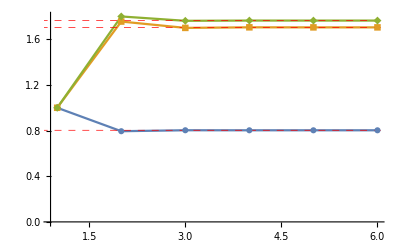

```mathematica
ListPlot[nestFind[#,5]&/@{1,2,3},PlotRange->All,Joined->True,PlotMarkers->Automatic,GridLines->{{},Eigenvalues[H]},GridLinesStyle->Directive[Dashed, Red,Thick]]
```

```mathematica
Eigenvectors[H][[-1,;;3]]
```

{0.140622-0.61729 ⅈ,-0.409803+0.156891 ⅈ,-0.411985+0.446325 ⅈ}

```mathematica
H.Eigenvectors[H][[-1]]-0.8024257379193809Eigenvectors[H][[-1]]//Chop
```

{0,0,0,0,0,0}

```mathematica
Norm[Heff[0.8024257379193809].Eigenvectors[H][[-1,;;3]]-0.8024257379193809Eigenvectors[H][[-1,;;3]]]
```

1.73022×10^-15

```mathematica
Norm[Heff[0.8024257379193809].Eigenvectors[Heff[0.8024257379193809]][[-1]]-0.8024257379193809Eigenvectors[Heff[0.8024257379193809]][[-1]]]
```

7.62145×10^-16

### The eigenvectors are not the same

```mathematica
Normalize@Eigenvectors[H][[-1,;;3]]
```

{-0.260722+0.488084 ⅈ,0.613316-0.22299 ⅈ,-0.352725+0.378817 ⅈ}

```mathematica
Eigenvalues[Heff[0.8024257379193809]]
```

{1.8076,1.76694,0.802426}

```mathematica
Eigenvectors[Heff[0.8024257379193809]][[3]]
```

{0.534879-0.141793 ⅈ,-0.581144-0.296906 ⅈ,0.517607+0. ⅈ}

```mathematica
Eigenvectors[H][[-1,;;3]]-T01.Inverse[ϵ IdentityMatrix[3]-H11].Eigenvectors[H][[-1,4;;]]/.ϵ->0.8024257379193809
```

{-0.242811+0.456949 ⅈ,0.58167-0.212008 ⅈ,-0.333034+0.354988 ⅈ}